```mathematica
Clear["Global`*"]
```

```mathematica
en=1000;(*系综*)
```

```mathematica
dt=0.01;t=5;(*时间*)
(*参数*)
len=IntegerPart[t/dt];
γ=1;Vp=40;
x0=0.1;v0=0;
sigma=20;
```

```mathematica
tlist=Table[dt*n,{n,1,len}];(*时间标号*)
Xlist=Table[0,len];(*x(t)标号*)
```

```mathematica
Table[{
x=x0;v=v0;xlist=Table[0,len];(*初始化x*)
list=RandomVariate[NormalDistribution[0,dt],len];(*产生随机参数*)
Table[{
v=v+(-γ*v+Vp*Sin[x])*dt+sigma*list[[n]];
x=x+v*dt,
xlist[[n]]=x

},{n,1,len}];(*迭代*)
Table[Xlist[[i]]=Xlist[[i]]+xlist[[i]],{i,1,len}];(*收集当前系统的解*)
},en];
Xlist=Xlist/en;
```

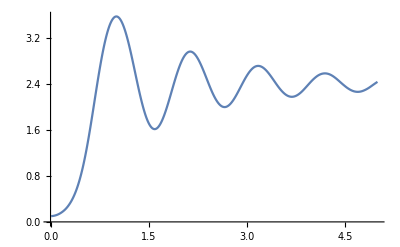

```mathematica
Transpose[{tlist,Xlist}]//ListLinePlot
```